```mathematica
SetDirectory[NotebookDirectory[]];
ExportFlag=False;
FigureOutPutFlag=False;
AllSouzu=Table[{},{i,47,55,1}];
AllOutPutMessage={};
Do[{
FolderNumber=DoFolderNumber;
(*FolderNumber=47;*)
data=Import["ShellBox_"<>ToString[FolderNumber]<>"/data.txt","Table"];
OutPutMessage={};
OutPutMessageTmp="FolderNumber"<>ToString[FolderNumber];
AppendTo[OutPutMessage,OutPutMessageTmp];

OutPutMessageTmp="行数は"<>ToString[Length[data]];
AppendTo[OutPutMessage,OutPutMessageTmp];
vallist={
(*列番号，名前，最小値，最大値，重複を除く配列の長さ，値を正規化(False：しない，True：する)，
正規化しない場合の最小値，正規化しない場合の最大値*)
{1,"σ",Infinity,-Infinity,0,False,0,1},
{2,"κ",Infinity,-Infinity,0,False,0,1},
{7,"MER",Infinity,-Infinity,0,False,0,1},
{9,"time",Infinity,-Infinity,0,True,0,1},
{11,"MVR",Infinity,-Infinity,0,True,0,1.5},
{13,"VMI",Infinity,-Infinity,0,False,0,1},
{14,"IVI",Infinity,-Infinity,0,False,0,1},
{15,"ExitCode",Infinity,-Infinity,0,False,1,3}
};
(**************************************)
For[i=1,i≤Length[vallist],i++,
{
tmp=Table[{
data[[j,vallist[[i,1]]]]
},{j,1,Length[data]}];
vallist[[i,3]]=Min[tmp];
vallist[[i,4]]=Max[tmp];
pmin=ToString[TraditionalForm[vallist[[i,3]]]];
pmax=ToString[TraditionalForm[vallist[[i,4]]]];
OutPutMessageTmp=vallist[[i,2]]<>"の(min,max)="<>"("<>pmin<>","<>pmax<>").";
AppendTo[OutPutMessage,OutPutMessageTmp];
}];
(**************************************)
For[i=1,i≤Length[vallist],i++,
{
tmp=Table[{
data[[j,vallist[[i,1]]]]
},{j,1,Length[data]}];
vallist[[i,5]]=DeleteDuplicates[tmp]//Sort//Flatten//Length;
plen=ToString[vallist[[i,5]]];
OutPutMessageTmp=vallist[[i,2]]<>"のデータ長は"<>plen;
AppendTo[OutPutMessage,OutPutMessageTmp];
}];
(**************************************)
(*Judge dx*)
i=1;
tmp=Table[{
data[[j,vallist[[i,1]]]]
},{j,1,Length[data]}];
tmpData=DeleteDuplicates[tmp]//Sort//Flatten;
iVSLen=tmpData;
Imax=Length[tmpData];
dx=(Max[tmpData]-Min[tmpData])/(Imax-1);
OutPutMessageTmp="dx="<>ToString[dx];
AppendTo[OutPutMessage,OutPutMessageTmp];
(*dy*)
i=2;
tmp=Table[{
data[[j,vallist[[i,1]]]]
},{j,1,Length[data]}];
tmpData=DeleteDuplicates[tmp]//Sort//Flatten;
iVSVol=tmpData;
Jmax=Length[tmpData];
dy=(Max[tmpData]-Min[tmpData])/(Jmax-1);
OutPutMessageTmp="dy="<>ToString[dy];
AppendTo[OutPutMessage,OutPutMessageTmp];
(*MERが最小値のσとκを表示*)
σκz=
Table[{
data[[j,vallist[[1,1]]]],
data[[j,vallist[[2,1]]]],
data[[j,vallist[[3,1]]]]
},{j,1,Length[data]}];
{x,y,z}=Sort[σκz,#1[[3]]<#2[[3]]&][[1]];
OutPutMessageTmp="(σ,κ)=("<>ToString[CForm[x]]<>","<>ToString[CForm[y]]<>")";
AppendTo[OutPutMessage,OutPutMessageTmp];
AppendTo[AllOutPutMessage,OutPutMessage];
Table[Print[OutPutMessage[[i]]],{i,1,Length[OutPutMessage],1}]

(**************************************)
If[FigureOutPutFlag,
{
SouzuList={};
For[k=3,k≤0+1*Length[vallist],k++,{
σκz=
Table[{
data[[j,vallist[[1,1]]]],
data[[j,vallist[[2,1]]]],
data[[j,vallist[[k,1]]]]
},{j,1,Length[data]}];
Souzu={};
For[l=1,l≤Length[data],l++,{
{x,y,z}=σκz[[l]];
ix=Position[iVSLen,x][[1,1]];
idx=1;
If[Abs[iVSLen[[ix]]-x],Print["Error!!"]];
iy=Position[iVSVol,y][[1,1]];
If[Abs[iVSLen[[iy]]-y],Print["Error!!"]];
idy=1;
Sikaku={
{ix-idx/2,iy-idy/2},
{ix+idx/2,iy-idy/2},
{ix+idx/2,iy+idy/2},
{ix-idx/2,iy+idy/2}
};
If[vallist[[k,6]],
HueColor=2/3(1-(z-vallist[[k,3]])/(vallist[[k,4]]-vallist[[k,3]])),
HueColor=2/3(1-(z-vallist[[k,7]])/(vallist[[k,8]]-vallist[[k,7]]))
];
AppendTo[Souzu,{Hue[HueColor],Polygon[Sikaku]}];
}];
(*MERが最小値の箇所を黒枠で表示*)
{x,y,z}=Sort[σκz,#1[[3]]<#2[[3]]&][[1]];
ix=Position[iVSLen,x][[1,1]];
idx=1;
If[Abs[iVSLen[[ix]]-x],Print["Error!!"]];
iy=Position[iVSVol,y][[1,1]];
If[Abs[iVSLen[[iy]]-y],Print["Error!!"]];
AppendTo[Souzu,{RGBColor[0,0,0],Line[
{
{ix-idx/2,iy-idy/2},
{ix+idx/2,iy-idy/2},
{ix+idx/2,iy+idy/2},
{ix-idx/2,iy+idy/2},
{ix-idx/2,iy-idy/2}
}]}];
gra=Graphics[Souzu,AspectRatio->1];
If[ExportFlag,
Export["相図"<>ToString[FolderNumber]<>"-"<>ToString[k]<>"_"<>vallist[[k,2]]<>"-"<>".png",Rasterize[gra,ImageSize->500,ImageResolution->500]];
];
AppendTo[SouzuList,gra];
}];
AllSouzu[[DoFolderNumber-46]]=SouzuList;
}];
},{DoFolderNumber,47,55,1}]
```

FolderNumber47

行数は10000

σの(min,max)=(1.×10^-14,0.1).

κの(min,max)=(1.×10^-14,0.1).

MERの(min,max)=(0.572962,0.935257).

timeの(min,max)=(1.999,9769.4369999999999).

MVRの(min,max)=(0.974599,1.20213).

VMIの(min,max)=(3.02×10^-13,0.0314632).

IVIの(min,max)=(8.×10^-14,0.0231003).

ExitCodeの(min,max)=(1.,2.).

σのデータ長は100

κのデータ長は100

MERのデータ長は9931

timeのデータ長は2145

MVRのデータ長は9645

VMIのデータ長は7013

IVIのデータ長は733

ExitCodeのデータ長は2

dx=0.0010101

dy=0.0010101

(σ,κ)=(0.012045035402588,0.000585702081806)

FolderNumber48

行数は10000

σの(min,max)=(1.×10^-14,0.1).

κの(min,max)=(1.×10^-14,0.1).

MERの(min,max)=(0.646224,0.968495).

timeの(min,max)=(9.717,8012.8119999999999).

MVRの(min,max)=(0.972834,1.20151).

VMIの(min,max)=(1.89×10^-13,0.00125123).

IVIの(min,max)=(8.3×10^-14,9.99315×10^-6).

ExitCodeの(min,max)=(1.,2.).

σのデータ長は100

κのデータ長は100

MERのデータ長は9956

timeのデータ長は2497

MVRのデータ長は9699

VMIのデータ長は6975

IVIのデータ長は323

ExitCodeのデータ長は2

dx=0.0010101

dy=0.0010101

(σ,κ)=(0.006579332246576,8.497534359e-6)

FolderNumber49

行数は10000

σの(min,max)=(1.×10^-14,0.1).

κの(min,max)=(1.×10^-14,0.1).

MERの(min,max)=(0.582013,0.963554).

timeの(min,max)=(1.213,10457.65200000000004).

MVRの(min,max)=(0.974747,1.20412).

VMIの(min,max)=(1.51×10^-13,0.0347244).

IVIの(min,max)=(7.8×10^-14,0.0523467).

ExitCodeの(min,max)=(1.,2.).

σのデータ長は100

κのデータ長は100

MERのデータ長は9910

timeのデータ長は1883

MVRのデータ長は9635

VMIのデータ長は7165

IVIのデータ長は507

ExitCodeのデータ長は2

dx=0.0010101

dy=0.0010101

(σ,κ)=(0.004862601580065,0.001450828778496)

FolderNumber50

行数は10000

σの(min,max)=(1.×10^-14,0.1).

κの(min,max)=(1.×10^-14,0.1).

MERの(min,max)=(0.301125,0.962189).

timeの(min,max)=(2.251,26403.71600000000035).

MVRの(min,max)=(0.974792,1.20466).

VMIの(min,max)=(4.41×10^-13,0.0226801).

IVIの(min,max)=(7.5×10^-14,0.017874).

ExitCodeの(min,max)=(1.,2.).

σのデータ長は100

κのデータ長は100

MERのデータ長は9934

timeのデータ長は2059

MVRのデータ長は9668

VMIのデータ長は6914

IVIのデータ長は582

ExitCodeのデータ長は2

dx=0.0010101

dy=0.0010101

(σ,κ)=(0.002656087782947,0.000432876128108)

FolderNumber51

行数は10000

σの(min,max)=(1.×10^-14,0.1).

κの(min,max)=(1.×10^-14,0.1).

MERの(min,max)=(0.399073,0.960624).

timeの(min,max)=(1.65,20361.13999999999942).

MVRの(min,max)=(0.97568,1.20407).

VMIの(min,max)=(0.,0.0169095).

IVIの(min,max)=(8.1×10^-14,0.033132).

ExitCodeの(min,max)=(1.,2.).

σのデータ長は100

κのデータ長は100

MERのデータ長は9906

timeのデータ長は1768

MVRのデータ長は9659

VMIのデータ長は6907

IVIのデータ長は552

ExitCodeのデータ長は2

dx=0.0010101

dy=0.0010101

(σ,κ)=(0.003593813663805,0.000585702081806)

FolderNumber52

行数は10000

σの(min,max)=(1.×10^-14,0.1).

κの(min,max)=(1.×10^-14,0.1).

MERの(min,max)=(0.366787,0.938279).

timeの(min,max)=(1.121,20566.16900000000169).

MVRの(min,max)=(0.976919,1.20404).

VMIの(min,max)=(0.,0.0408956).

IVIの(min,max)=(7.1×10^-14,0.0576965).

ExitCodeの(min,max)=(1.,2.).

σのデータ長は100

κのデータ長は100

MERのデータ長は9919

timeのデータ長は1765

MVRのデータ長は9611

VMIのデータ長は7022

IVIのデータ長は541

ExitCodeのデータ長は2

dx=0.0010101

dy=0.0010101

(σ,κ)=(0.004862601580065,0.001450828778496)

FolderNumber53

行数は10000

σの(min,max)=(1.×10^-14,1.).

κの(min,max)=(1.×10^-14,0.1).

MERの(min,max)=(0.249784,0.693398).

timeの(min,max)=(0.068,5795.4350000000004).

MVRの(min,max)=(0.925175,1.20216).

VMIの(min,max)=(0.,22.3222).

IVIの(min,max)=(8.×10^-14,0.186207).

ExitCodeの(min,max)=(1.,2.).

σのデータ長は100

κのデータ長は100

MERのデータ長は9126

timeのデータ長は677

MVRのデータ長は8700

VMIのデータ長は7196

IVIのデータ長は67

ExitCodeのデータ長は2

dx=0.010101

dy=0.0010101

(σ,κ)=(0.722080901838548,0.001450828778496)

FolderNumber54

行数は10000

σの(min,max)=(1.×10^-14,1.).

κの(min,max)=(1.×10^-14,0.1).

MERの(min,max)=(0.286862,0.801262).

timeの(min,max)=(0.067,95.417).

MVRの(min,max)=(0.92613,1.2016).

VMIの(min,max)=(9.99325×10^-6,6.72551).

IVIの(min,max)=(8.3×10^-14,0.185905).

ExitCodeの(min,max)=(1.,2.).

σのデータ長は100

κのデータ長は100

MERのデータ長は9227

timeのデータ長は488

MVRのデータ長は8781

VMIのデータ長は5325

IVIのデータ長は68

ExitCodeのデータ長は2

dx=0.010101

dy=0.0010101

(σ,κ)=(0.722080901838548,0.00107226722201)

FolderNumber55

行数は10000

σの(min,max)=(1.×10^-14,1.).

κの(min,max)=(1.×10^-14,0.1).

MERの(min,max)=(0.254675,0.687856).

timeの(min,max)=(0.068,136.84399999999999).

MVRの(min,max)=(0.927567,1.20419).

VMIの(min,max)=(9.99832×10^-6,5.57772).

IVIの(min,max)=(7.8×10^-14,0.187876).

ExitCodeの(min,max)=(1.,2.).

σのデータ長は100

κのデータ長は100

MERのデータ長は9054

timeのデータ長は447

MVRのデータ長は8685

VMIのデータ長は6111

IVIのデータ長は69

ExitCodeのデータ長は2

dx=0.010101

dy=0.0010101

(σ,κ)=(0.722080901838548,0.001450828778496)

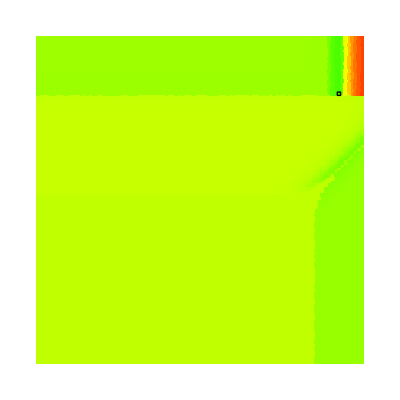
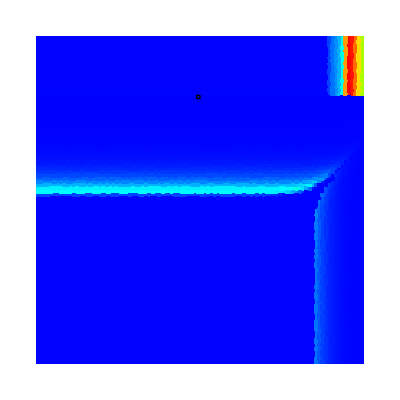
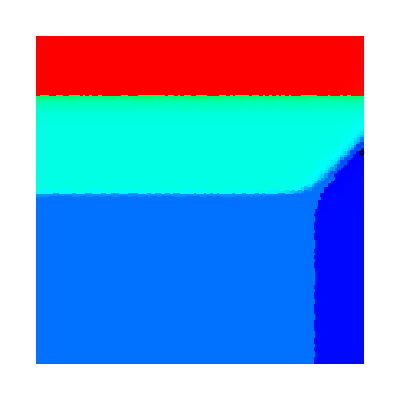
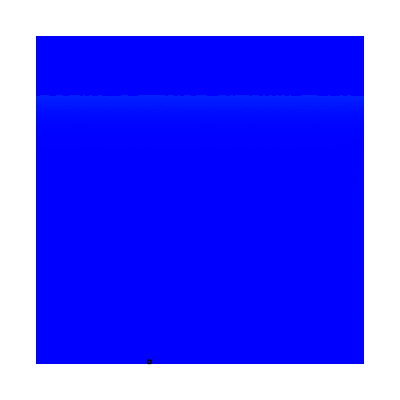
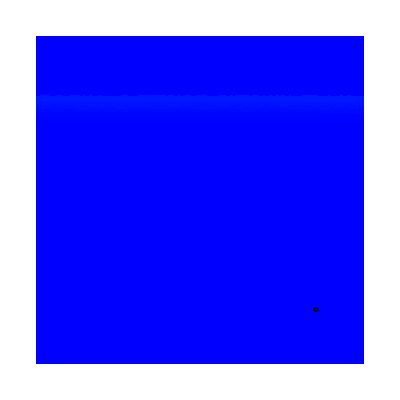
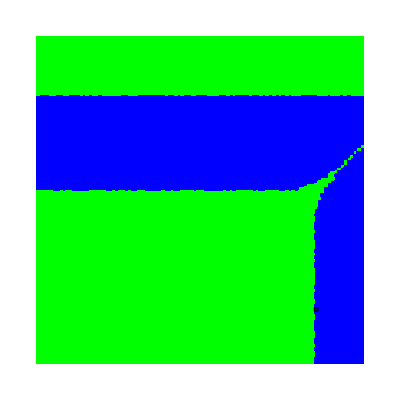

```mathematica
AllSouzu[[1]]
```

```mathematica
Table[{OutPutMessage[[1]],OutPutMessage[[21]]},{i,1,6}]
```

{{FolderNumber55,(σ,κ)=(0.722080901838548,0.001450828778496)},{FolderNumber55,(σ,κ)=(0.722080901838548,0.001450828778496)},{FolderNumber55,(σ,κ)=(0.722080901838548,0.001450828778496)},{FolderNumber55,(σ,κ)=(0.722080901838548,0.001450828778496)},{FolderNumber55,(σ,κ)=(0.722080901838548,0.001450828778496)},{FolderNumber55,(σ,κ)=(0.722080901838548,0.001450828778496)}}

```mathematica
Table[{i,AllOutPutMessage[[i,1]],AllOutPutMessage[[i,21]]},{i,1,Length[AllOutPutMessage]}]
```

{{1,FolderNumber47,(σ,κ)=(0.012045035402588,0.000585702081806)},{2,FolderNumber48,(σ,κ)=(0.006579332246576,8.497534359e-6)},{3,FolderNumber49,(σ,κ)=(0.004862601580065,0.001450828778496)},{4,FolderNumber50,(σ,κ)=(0.002656087782947,0.000432876128108)},{5,FolderNumber51,(σ,κ)=(0.003593813663805,0.000585702081806)},{6,FolderNumber52,(σ,κ)=(0.004862601580065,0.001450828778496)},{7,FolderNumber53,(σ,κ)=(0.722080901838548,0.001450828778496)},{8,FolderNumber54,(σ,κ)=(0.722080901838548,0.00107226722201)},{9,FolderNumber55,(σ,κ)=(0.722080901838548,0.001450828778496)}}

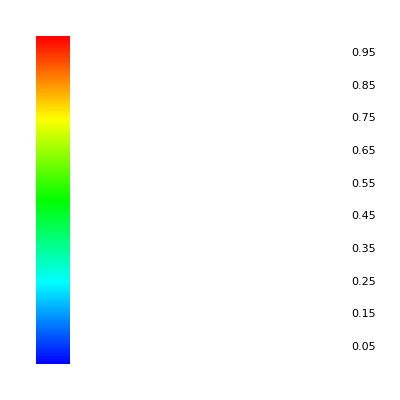
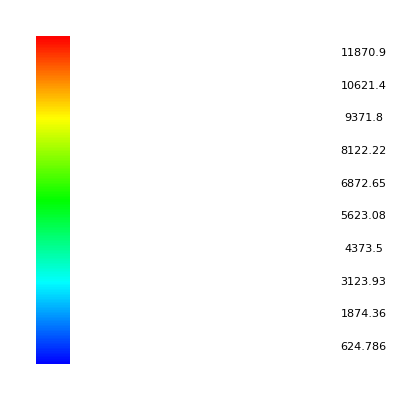
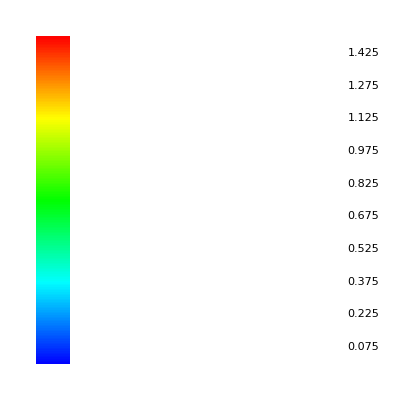
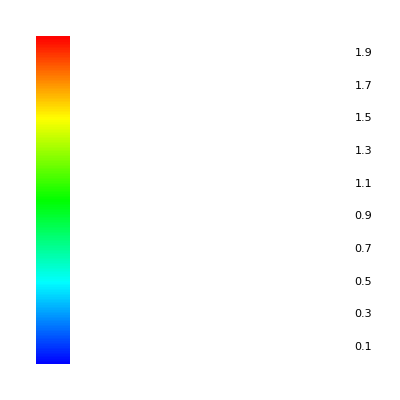
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*カラーバー*)
ColorBar={};
(*帯の作成*)
Imax=200;
ddx=1/Imax;
For[i=1,i≤Imax,i++,
{
Sq=
{
{0,ddx*(i-1)},
{20ddx,ddx*(i-1)},
{20ddx,ddx*i},
{0,ddx*i}
};
z=ddx*(i-0.5);
HueColor=2/3(1-z);
AppendTo[ColorBar,{Hue[HueColor],Polygon[Sq]}]
}];
ColorBar=Graphics[ColorBar];
TextBarList={};
For[k=3,k≤0+1*Length[vallist],k++,{
(*帯の文字の作成*)
TextBar={};
Imax=10;
If[vallist[[k,6]],
{zmin=vallist[[k,3]],zmax=vallist[[k,4]]},
{zmin=vallist[[k,7]],zmax=vallist[[k,8]]}
];
dz=(zmax-zmin)/Imax;
dh=1/Imax;
For[i=1,i≤Imax,i++,
{
z=dz*(i-0.5);
h=dh*(i-0.5);
AppendTo[TextBar,Text[ToString[z],{1,h}]]
}];
ColorTextBar=Show[Graphics[TextBar],ColorBar];
AppendTo[TextBarList,ColorTextBar];

Export["カラーバー"<>ToString[FolderNumber]<>"-"<>ToString[k]<>"_"<>vallist[[k,2]]<>"-"<>".png",Rasterize[ColorTextBar,ImageSize->50,ImageResolution->500]];
}]
TextBarList
```

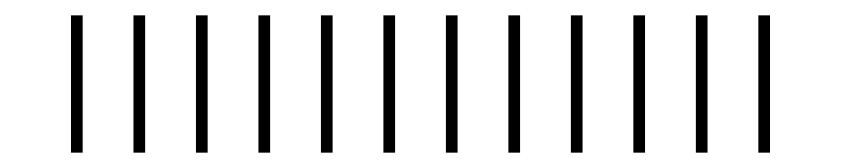

(1.×10^-14
1.5×10^-13
2.3×10^-12
3.5×10^-11
5.3×10^-10
8.1×10^-9
1.2×10^-7
1.9×10^-6
0.000028
0.00043
0.0066
0.1)

(0.1
0.0066
0.00043
0.000028
1.9×10^-6
1.2×10^-7
8.1×10^-9
5.3×10^-10
3.5×10^-11
2.3×10^-12
1.5×10^-13
1.×10^-14)

```mathematica
(*スケール*)
xMin=1*10^(-14);
xMax=1*10^(-1);
imax=100;
r=(xMax/xMin)^(1/(imax-1));
iVSx=Table[xMin*r^i,{i,0,99,1}];
xAxesGrid={};
xAxesText={};
For[i=1,i≤Length[iVSx],i+=9,
{
x=iVSx[[i]];
y=0.0;
yHaba=1.0;
g=Graphics[
{Thickness[10^-2],
Line[{
{Log[x],y},
{Log[x],y+yHaba}
}]}
];
AppendTo[xAxesGrid,g];
g=N[x,2];
AppendTo[xAxesText,g];
}]
xAxesGridg=Show[xAxesGrid]
xAxesText//MatrixForm
xAxesText//Reverse//MatrixForm
```

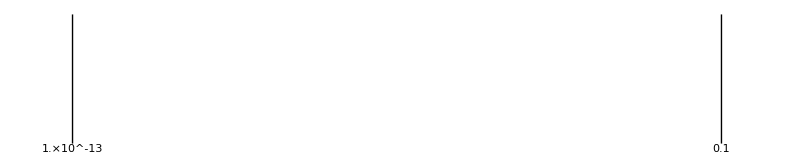

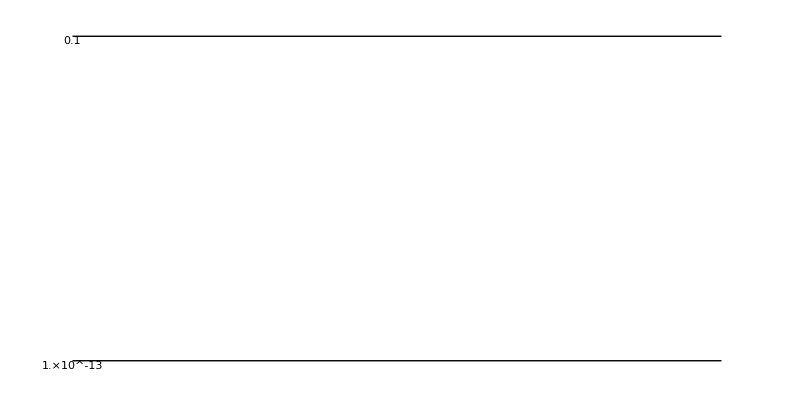

```mathematica
(*スケール*)
xMin=1.0*10^(-14);
xMax=1.0*10^(-1);
imax=100;
r=(xMax/xMin)^(1/(imax-1));
iVSx=Table[xMin*r^i,{i,0,99,1}];
xAxes={};
For[i=1,i≤Length[iVSx],i+=9,
{
x=iVSx[[i]];
y=0.0;
yHaba=0.1;
g=Graphics[
{
Text[ToString[TraditionalForm[x]],{Log[x],y},{Center,Top}]
,
Line[{
{Log[x],y},
{Log[x],y+yHaba}
}]

}];
AppendTo[xAxes,g]
}]
xAxesg=Show[xAxes]

yAxes={};
For[i=1,i≤Length[iVSVol],i+=9,
{
y=iVSVol[[i]];
x=0.0;
xHaba=0.1;
g=Graphics[
{
Text[ToString[TraditionalForm[y]],{x,Log[y]},{Center,Top}]
,
Line[{
{x,Log[y]},
{x+xHaba,Log[y]}
}]

}];
AppendTo[yAxes,g]
}]
yAxesg=Show[yAxes,AspectRatio->0.5]
```

```mathematica
OutPutMessage
```

{行数は10000,σの(min,max)=(1.×10^-14,0.9).,κの(min,max)=(1.×10^-14,0.1).,MERの(min,max)=(0.572275,0.999069).,timeの(min,max)=(0.19,9776.14400000000023).,MVRの(min,max)=(0.966438,1.20213).,VMIの(min,max)=(0.,0.0808732).,IVIの(min,max)=(8.×10^-14,0.161154).,ExitCodeの(min,max)=(1.,2.).}

```mathematica
Exp[14]
10.^(14/99)
```

ⅇ^14

1.38489

```mathematica
r=10.^(14/99)
```

1.38489

```mathematica
r=10.^(13/99)
r0=10^(-14);
Table[r0*r^(i),{i,0,99}]
```

1.35305

{1.×10^-14,1.35305×10^-14,1.83074×10^-14,2.47708×10^-14,3.3516×10^-14,4.53488×10^-14,6.13591×10^-14,8.30218×10^-14,1.12332×10^-13,1.51991×10^-13,2.05651×10^-13,2.78256×10^-13,3.76494×10^-13,5.09414×10^-13,6.89261×10^-13,9.32603×10^-13,1.26186×10^-12,1.70735×10^-12,2.31013×10^-12,3.12572×10^-12,4.22924×10^-12,5.72237×10^-12,7.74264×10^-12,1.04762×10^-11,1.41747×10^-11,1.91791×10^-11,2.59502×10^-11,3.51119×10^-11,4.75081×10^-11,6.42807×10^-11,8.69749×10^-11,1.17681×10^-10,1.59228×10^-10,2.15443×10^-10,2.91505×10^-10,3.94421×10^-10,5.3367×10^-10,7.22081×10^-10,9.7701×10^-10,1.32194×10^-9,1.78865×10^-9,2.42013×10^-9,3.27455×10^-9,4.43062×10^-9,5.99484×10^-9,8.11131×10^-9,1.0975×10^-8,1.48497×10^-8,2.00923×10^-8,2.71859×10^-8,3.67838×10^-8,4.97702×10^-8,6.73415×10^-8,9.11163×10^-8,1.23285×10^-7,1.6681×10^-7,2.25702×10^-7,3.05386×10^-7,4.13201×10^-7,5.59081×10^-7,7.56463×10^-7,1.02353×10^-6,1.38489×10^-6,1.87382×10^-6,2.53536×10^-6,3.43047×10^-6,4.64159×10^-6,6.28029×10^-6,8.49753×10^-6,0.0000114976,0.0000155568,0.000021049,0.0000284804,0.0000385353,0.0000521401,0.000070548,0.0000954548,0.000129155,0.000174753,0.000236449,0.000319927,0.000432876,0.000585702,0.000792483,0.00107227,0.00145083,0.00196304,0.00265609,0.00359381,0.0048626,0.00657933,0.00890215,0.012045,0.0162975,0.0220513,0.0298365,0.0403702,0.0546228,0.0739072,0.1}